## Figure 6A, 6B

Evaluate notebook to produce plots from Fig. 6A, 6B. (one example of approximate vs. perfect trade-offs)

```mathematica
Clear["Global`*"]; 
precision=30;
$MinPrecision=precision;
SetDirectory[NotebookDirectory[]];
```

### Statics

```mathematica
getPositions[pop0_]:=
Block[{m0,list,extendedPop},
m0=Length[pop0];
extendedPop=Join[{0},pop0];
Table[{Total[extendedPop[[1;;i-1]]],Total[extendedPop[[1;;i]]]},{i,2,m0+1}]
];

getConcentration[n_,nutrient_]:=
Block[{i,m0,c,dc,m,cSys,cSysWrap,cSystem,dcSys,dcSysWrap,dcSystem,totalcSys,vars,aVars,bVars,z},
m0=Length[n];
aVars=ToExpression[Table["a"<>IntegerString[k],{k,m0}]];
bVars=ToExpression[Table["b"<>IntegerString[k],{k,m0}]];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
dc[a_,b_,α_,θ_]:=Sqrt[α/d]*(a*E^(Sqrt[α/d]*θ)-b*E^(-Sqrt[α/d]*θ));

(*  Create a system of eqs for c(θ) in each region *)
cSys=Table[c[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==c[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
cSysWrap=c[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==c[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
cSystem=Join[cSys,{cSysWrap}];

(*do the same thing for the derivatives of c(θ)*)
dcSys=Table[dc[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==dc[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
dcSysWrap=dc[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==dc[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
dcSystem=Join[dcSys,{dcSysWrap}];

totalcSys=Join[cSystem,dcSystem];
vars=Table[{aVars[[i]],bVars[[i]]},{i,m0}]//Flatten;
{z,m}=CoefficientArrays[totalcSys,vars];
LinearSolve[m,-z]  
];
(*returns {a1,b1,a2,b2...}: in a region σ c_i=a*E^(a*θ/d)+b*E^(-a*θ/d)+si/αi. *)

fullConcentration[n_,nutrient_]:=
Block[{a,b,c,coeff,positions,pieces,conditions,fullC},
coeff=getConcentration[n,nutrient];
positions=getPositions[n];
a=Table[coeff[[2*i-1]],{i,m}];
b=Table[coeff[[2*i]],{i,m}];
c[a_,b_,α_,θ_]:=a*E^(Sqrt[α/d]*θ)+b*E^(-Sqrt[α/d]*θ)+s[[nutrient]]/α;
pieces=Table[c[a[[j]],b[[j]],α[[j,nutrient]],theta-positions[[j,1]]],{j,m}];
conditions=Table[positions[[i,1]]<theta<=positions[[i,2]],{i,m}];
fullC=Piecewise[Transpose[{pieces,conditions}]]
];
```

### Define some constants

```mathematica
supply=1;  (*total nutrient supply*)
δ=supply;
e=1;             (* total enzyme budget*)
steps=20000;
```

### Numeric parameters

```mathematica
d=1; //N(*diffusion coefficient*)
l=Sqrt[10]//N;
s1=0.4;
s2=supply-s1;
s={s1,s2};

seed=360;
SeedRandom[seed];
```

```mathematica
m=10;
noiseLevel=.005;
budgets=RandomVariate[NormalDistribution[1,noiseLevel],m];
```

```mathematica
alphas=Table[RandomReal[budgets[[i]]],{i,m}];
α=Table[{alphas[[i]],budgets[[i]]-alphas[[i]]},{i,m}];
```

```mathematica
strat=Table[α[[i,1]],{i,m}];   (*maps strategies to continuum of nutrient 1, nutrient 2*)
sScaled=(e/Total[s])*s[[1]];
```

```mathematica
extremeBudgets=2*(budgets-e)+e;
budgets=extremeBudgets;
```

```mathematica
alphaProp=Table[alphas[[i]]/budgets[[i]],{i,m}];
αProp=Table[{alphaProp[[i]],e-alphaProp[[i]]},{i,m}];
```

### get colorscheme data

```mathematica
(*Read in the numerical data*)Get["https://pastebin.com/raw/gN4wGqxe"]
ParulaCM=With[{colorlist=RGBColor@@@parulaColors},Blend[colorlist,#]&];
Cube1CM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
CubeYFCM=With[{colorlist=RGBColor@@@cubeYFColors},Blend[colorlist,#]&];
LinearLCM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
JetCM=With[{colorlist=RGBColor@@@jetColors},Blend[colorlist,#]&];
```

```mathematica
colors=LinearLCM/@alphaProp;
```

### Dynamics

```mathematica
getGrowth[pop_,species_,c_]:=
Block[{growth,myN,myA,myB},
myN=pop[[species]];
myA=c[[species*2-1]];
myB=c[[species*2]];

growth=Table[α[[species,i]]*((s[[i]]*myN/α[[species,i]])+Sqrt[d/α[[species,i]]]*(myA[[i]]*(E^(myN*Sqrt[α[[species,i]]/d])-1)-myB[[i]]*(E^(-myN*Sqrt[α[[species,i]]/d])-1))),{i,2}]//Total
];
```

```mathematica
ndot[n_?(VectorQ[#, NumericQ]&)]:=
Block[{dn,growthTable,n0,nNew,cCoeff},
n0=n;
cCoeff=Transpose[{getConcentration[n0,1],getConcentration[n0,2]}];
growthTable=Table[getGrowth[n0,i,cCoeff],{i,Length[n0]}];
(*δ=Total[growthTable];*)
dn=growthTable-δ*n0
];
```

## Approximate trade-offs

### Spatial

```mathematica
nInit=l*ConstantArray[1/m,m]//N;
```

```mathematica
sol1=NDSolveValue[{n'[t]==ndot[n[t]],n[0]==nInit},n,{t,0,steps}];
```

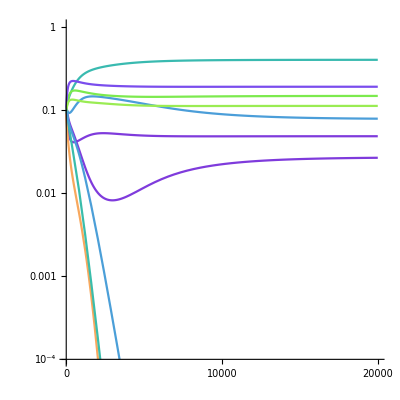

```mathematica
logSeriesPlot1=LogPlot[Evaluate[Table[Indexed[sol1[t],i]/l,{i,m}]],{t,0,steps},PlotRange->{{0,steps},{10^-4,1}},Ticks->{Range[0,20000,10000],{.0001,.001,.01,.1,1}},TicksStyle->Black,PlotStyle->colors,LabelStyle->Directive[Black,16],AspectRatio->1]
```

```mathematica
Export["fig6B_right_spatialTimeseries.svg",%,"SVG"];
```

### Well-mixed

```mathematica
growthRate[pops_,thisSpecies_]:=
Module[{thisDiversity,thisStrat,interactionNutrient1,interactionNutrient2,growth,thisSpeciesPosition},
thisDiversity=Length[pops];
thisStrat=α[[thisSpecies]];

interactionNutrient1=Sum[pops[[i]]*α[[i,1]],{i,thisDiversity}];
interactionNutrient2=Sum[pops[[i]]*α[[i,2]],{i,thisDiversity}];

growth=(thisStrat[[1]]*s1/interactionNutrient1+thisStrat[[2]]*s2/interactionNutrient2)*pops[[thisSpecies]]
];
```

```mathematica
evolveN[n_?(VectorQ[#, NumericQ]&)]:=
Block[{dn,growthTable,positions,n0,nNew},
n0=n;
growthTable=Table[growthRate[n0,i],{i,Length[n0]}];
dn=growthTable-δ*n0
];
```

```mathematica
wmStep=10000;
wellMixedInit=ConstantArray[1/m,m];
```

```mathematica
wellMixedSol=NDSolveValue[{n'[t]==evolveN[n[t]],n[0]==wellMixedInit},n,{t,0,wmStep},InterpolationOrder->All];
```

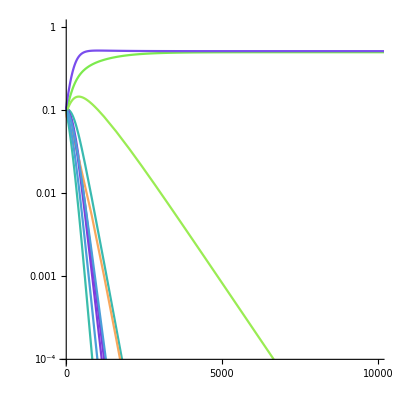

```mathematica
wellMixedLogSeriesPlot=LogPlot[Evaluate[Table[Indexed[wellMixedSol[t],i],{i,m}]],{t,0,steps},PlotRange->{{0,wmStep},{10^-4,1}},Ticks->{Range[0,10000,5000],{.0001,.001,.01,.1,1}},TicksStyle->Black,PlotStyle->colors,LabelStyle->Directive[Black,16],AspectRatio->1]
```

```mathematica
Export["fig6B_center_wellMixedTimeseries.svg",%,"SVG"];
```

## Exact trade-offs

### Visualize strategies

```mathematica
α=αProp;
```

```mathematica
p=Table[{Graphics[{EdgeForm[{Black}],FaceForm[colors[[i]]],Disk[]}],.05},{i,m}];
```

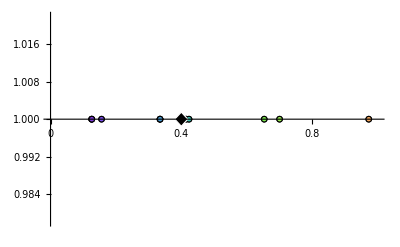

```mathematica
Show[ListPlot[Table[{{α[[i,1]],e}},{i,m}],PlotMarkers->p,Ticks->{{0,.2,.4,.6,.8,1},Automatic},TicksStyle->Black,AxesOrigin->{0,1},PlotRange->{{0,e},{e-.022,e+.022}},LabelStyle->Directive[Black,14]],Graphics[{EdgeForm[{White}],Polygon[{{.4-.02,1},{.4,1+.0015},{.4+.02,1},{.4,1-.0015}}]}],Method->{"AxesInFront"->False}]
```

```mathematica
Export["fig6A_left_strategies.svg",%,"SVG"];
```

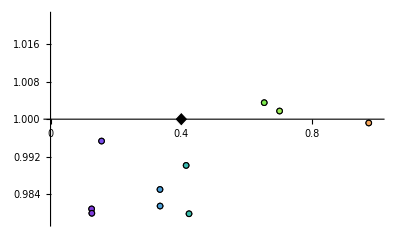

```mathematica
Show[ListPlot[Table[{{α[[i,1]],budgets[[i]]}},{i,m}],PlotMarkers->p,Ticks->{{0,.2,.4,.6,.8,1},Automatic},TicksStyle->Black,AxesOrigin->{0,1},PlotRange->{{0,e},{e-.022,e+.022}},LabelStyle->Directive[Black,14]],Graphics[{EdgeForm[{White}],Polygon[{{.4-.02,1},{.4,1+.0015},{.4+.02,1},{.4,1-.0015}}]}],Method->{"AxesInFront"->False}]
```

```mathematica
Export["fig6B_left_strategies.svg",%,"SVG"];
```

### Spatial

```mathematica
steps=20000;
```

```mathematica
nInit=l*ConstantArray[1/m,m]//N;
```

```mathematica
sol1=NDSolveValue[{n'[t]==ndot[n[t]],n[0]==nInit},n,{t,0,steps}];
```

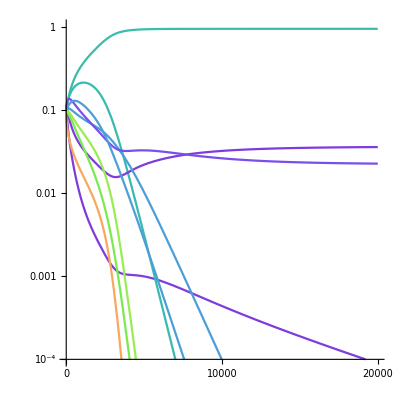

```mathematica
logSeriesPlot1=LogPlot[Evaluate[Table[Indexed[sol1[t],i]/l,{i,m}]],{t,0,steps},PlotRange->{{0,steps},{10^-4,1}},Ticks->{Range[0,40000,10000],{.0001,.001,.01,.1,1}},TicksStyle->Black,PlotStyle->colors,LabelStyle->Directive[Black,16],AspectRatio->1]
```

```mathematica
Export["fig6A_right_spatialTimeseries.svg",%,"SVG"];
```

### Well-mixed

```mathematica
s1=0.4;
s2=0.6;
```

```mathematica
s1=l*s1;
s2=l*s2;
```

```mathematica
growthRate[pops_,thisSpecies_]:=
Module[{thisDiversity,thisStrat,interactionNutrient1,interactionNutrient2,growth,thisSpeciesPosition},
thisDiversity=Length[pops];
thisStrat=α[[thisSpecies]];

interactionNutrient1=Sum[pops[[i]]*α[[i,1]],{i,thisDiversity}];
interactionNutrient2=Sum[pops[[i]]*α[[i,2]],{i,thisDiversity}];

growth=(thisStrat[[1]]*s1/interactionNutrient1+thisStrat[[2]]*s2/interactionNutrient2)*pops[[thisSpecies]]
];
```

```mathematica
evolveN[n_?(VectorQ[#, NumericQ]&)]:=
Block[{dn,growthTable,positions,n0,nNew},
n0=n;
growthTable=Table[growthRate[n0,i],{i,Length[n0]}];
dn=growthTable-δ*n0
];
```

```mathematica
wmStep=300;
wellMixedInit=l*ConstantArray[1/m,m];
```

```mathematica
wellMixedSol=NDSolveValue[{n'[t]==evolveN[n[t]],n[0]==wellMixedInit},n,{t,0,wmStep}];
```

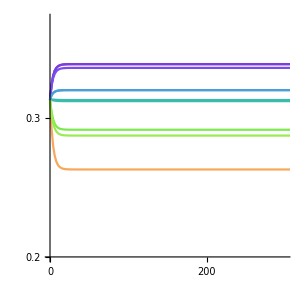

```mathematica
wellMixedLogSeriesPlot=LogPlot[Evaluate[Table[Indexed[wellMixedSol[t],i],{i,m}]],{t,0,steps},PlotRange->{{0,wmStep},{2*10^-1,.4}}(*,PlotLegends->SwatchLegend[{"n1","n2","n3","n4","n5","n6","n7","n8","n9","n10"}]*),Ticks->{Range[0,500,100],{.2,.3,.4}},TicksStyle->Black,PlotStyle->colors,LabelStyle->Directive[Black,16],PlotPoints->150,AspectRatio->.95]
```

```mathematica
Export["fig6A_center_wellMixedTimeseries.svg",%,"SVG"];
```